```mathematica
FullSimplify[Integrate[Sin[alpha]^2,{alpha,0,theta}]]
```

1

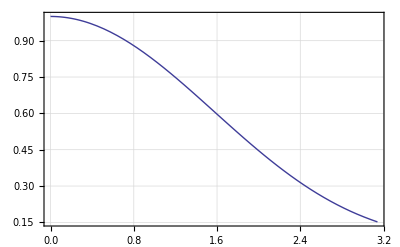

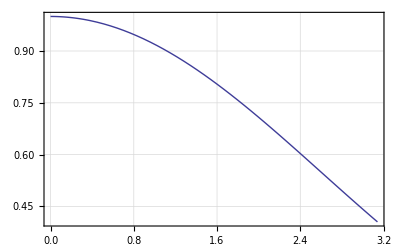

3 Sin[theta]^2

```mathematica
plotOpts={PlotRange -> All, Frame -> True, GridLines -> Automatic,PlotStyle-> Thick};
(* Plot[Sin[theta]/theta,{theta,0,Pi}, Evaluate[plotOpts]] *)

RRR=10;
Limit[3(1/2 (theta-Cos[theta] Sin[theta]))/theta^3,theta -> 0]
Plot[3(1/2 (theta-Cos[theta] Sin[theta]))/theta^3,{theta,10^-6,Pi}, Evaluate[plotOpts]]
Area[theta_]:=4*Pi*RRR^2*Sin[theta/2]^2;
Plot[4*Area[theta]/(4*Pi*RRR^2*theta^2),{theta,0,Pi}, Evaluate[plotOpts]]

FullSimplify[D[3(1/2 (theta-Cos[theta] Sin[theta])),theta]]

(* Plot[Area[theta]/Area[2*theta],{theta,0,Pi/2}, Evaluate[plotOpts]] *)
```

```mathematica
LLL=10;
AddL[x1_,x2_]:=Mod[x1+x2,LLL];
MultiplyL[x1_,x2_]:=Mod[x1,LLL]*Mod[x2,LLL];
AddS[s1_,s2_]:=Mod[s1+s2,LLL^2];

Print["AddL"];
AddL[1,3]
AddL[6,7]

Print["MultiplyL"];
MultiplyL[7,8]

Print["AddL distributivity"];
x1=6;
x2=7;
x3=8;

x23=AddL[x2,x3];
Print["x2+x3 = ",x23];

s1=MultiplyL[x1,AddL[x2,x3]];
s2=AddS[MultiplyL[x1,x2],MultiplyL[x1,x3]];

Print["x1*(x2+x3) = ",s1];
Print["x1*x2+x1*x3 = ",s2];
```